# Mathematica Notes

## Working with data

Dr. Liu Haohui

## Import & export

## Importing flat data

```mathematica
(* important large .xlsx file, imported as a list of matrices, corresponding to data from sheets*)
Needs["JLink`"];
ReinstallJava[JVMArguments -> "-Xmx1000m"]; (* default JVMArguments is 512 Mb, change this number to get larger memory *)
(* pick sheet number here or Flatten it afterwards *)
data=Import["Denver201401b.xlsx"][[sheetNumber,;;,;;]];
```

When importing comma limited datas, use “CSV” instead of specifying Delimiters. “Table” is also a common format, but not for .csv data, it imports .csv data as strings. 
Take note that single row data may be imported as a list of list.

```mathematica
data=Import["file.txt","Table"];
data=Import["file.csv","CSV"];
```

Import data with other delimiters:

```mathematica
Import["data.csv","Table","FieldSeparators"->";"]
```

```mathematica
(* use SemanticImport to import as dataset *)
data=SemanticImport["201401.txt",Delimiters->","];
```

To import lists of strings, use ImportString:

```mathematica
heading=ImportString[Import["C:\\Users\\a0000548\\Documents\\Mathematica\\headings01.txt"],"CSV"];
(* Import only reads the whole thing as a string, ImportString converts it to matrix of strings, namely lists/tables, specify string format correctly, "Table" only recognize "\n" as separater, but "CSV" recognize both "\n" and "," as delimiter *)
```

There are other import functions like ReadList, BinaryReadList, and Get. 
When reading very large files, it may be necessary to read using a lower level function:

```mathematica
strR=OpenRead["C:\\Users\\test.txt"];
output={};
line=1;
While[line=!={},
line=ReadList[strR,{Record,Record,Record,Record},30,RecordSeparators->{"\t","\n"}][[1]];
AppendTo[output,line];];
```

## Importing multiple files and merge them:

Use FileNames to obtain folder or file names. Read multiple files and merge them by appending:

```mathematica
SetDirectory[FileNameJoin[{$UserDocumentsDirectory,"Mathematica"}]];
files=FileNames["2012"~~__~~".txt",{"C:\\subdirectory path"},2]; (* read files down to level 2, meaning files/subfolders in the subdirectory path and all the files in the subfolders *)
output=Drop[Import[#,"Table"],1]&/@files;
(* optional: Drop is used to get rid of title line *)
```

Define functions to read from multiple folders, or when there is more complicated operations needed:

```mathematica
folders=FileNames["2012"~~__~~"folder",{"Z:\\05 Data\\01 Sunspectra\\SINGAPORE SPECTRUM DATA\\[501]\\2015"}];
fnReadData[path_?StringQ]:=Module[{files,output={}},
SetDirectory[path];

files=FileNames[];
AppendTo[output,Drop[Import[#,"Table"],1]]&/@files;

SetDirectory[FileNameJoin[{$UserDocumentsDirectory,"Mathematica"}]];
Export["Singapore"<>StringReplace[FileBaseName[path],"-"->""]<>".csv",Flatten[output,1]];
Return[FileBaseName[path]<>" done"]
]
(* this function reads all the files in each subfolder and merge them, outputing one merged dataset for each subfolder *)
fnReadData/@folders
```

## Export

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"dataset.csv"}],Map[MapAt[DateString[#,{"Day","/","Month","/","Year"," ","Hour",":","Minute"}]&,#,1]&,data],"CSV"];

Export[FileNameJoin[{dir,title<>"_"<>year<>"-"<>month<>".png"}],plot];
```

## Cursory inspection of data quality

Check dimension of data. If the data is “ragged”, Dimensions will only count elements at level 1, instead of full data dimension.

```mathematica
Dimensions[{{a,b,c},{d,e},{f}}]
```

{3}

Even when dimensions are intact, missing values may be present as an empty string (“”), “NA”, extreme values, or other forms. In this case, write a simple function to test whether the data matches the required format.

```mathematica
badData[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]]||entry[[-1]]>40;
filteredData=DeleteCases[data,_?badData];
```

Alternatively:

```mathematica
badData=Cases[data,Except[{_String,_String,__Real}|{__String}]];
```

When suspecting that a data contains some non-numeric values, can use MemberQ to find out.

```mathematica
SelectFirst[data,MemberQ[#,_String]&]
```

Quick summary of data min, max and averages.

assuming first column of data contains index like timestamp.

```mathematica
Print[{Range[Length[title]],title,Flatten[{"min",Min/@Transpose[data[[All,2;;-1]]]}],Flatten[{"max",Max/@Transpose[data[[All,2;;-1]]]}],Flatten[{"mean",Mean[data[[All,2;;-1]]]}]}//TableForm]
```

## Manipulating data in general

Replace missing values using ReplaceAll:

```mathematica
data/.""->Missing["no value"];
(* /. usually stops at the largest subexpression, sometimes may need to use Replace and specify levels *)
data=Replace[data,"NaN"->Missing["NaN"],2];
```

Pick out rows or columns based on labels:

```mathematica
pickData=Cases[data,{"row label",__}];
pickData=Select[data,#[[1]]===1&&#[[2]]==="label A"&];
pickValue=Cases[data,{"row label",y_Real,__}->y]; (* return the value of y *)
```

When there are many columns, can refer to column number by names by defining an association:

```mathematica
index=AssociationThread[title->Range[Length[title]]];
```

Extract rows that have max value in a certain column

```mathematica
dat={{10,b,30},{100,a,40},{1000,b,10},{1000,b,70},{100,b,20},{10,b,70}};
dat~Extract~Position[#,Max@#]&@Part[datᵀ,3] //AbsoluteTiming(*column 3*)
```

{0.0000289,{{1000,b,70},{10,b,70}}}

or more simply:

```mathematica
MaximalBy[dat,#[[3]]&]//AbsoluteTiming
```

{0.0001465,{{1000,b,70},{10,b,70}}}

when max value resides in another list and need to extract corresponding position:

```mathematica
Extract[dat[[All,;;2]],Position[dat[[All,3]],n_/;n==Max[dat[[All,3]]]]]//AbsoluteTiming
```

{0.0000359,{{1000,b},{10,b}}}

## Comparing, extracting or merging data

Combining multiple lists by first column as index with an inner join:

This operation combines two lists with an inner join (only retain indices that both have). 
Yellow highlighted number = number of lists - 1. 
Need to make sure lists are regularly shaped and no duplicate keys are present, otherwise column will get mixed up (dimension is not regular).

```mathematica
Flatten[{#,Rest/@{##2}}]&@@@(Pick[#,Length@#>2]&/@GatherBy[Join[list1,list2,list3],First])
```

```mathematica
Flatten[{#,Rest/@{##2}}]&@@@(Pick[#,Length@#>1]&/@GatherBy[Join[list1,list2],First])
```

More generally:

```mathematica
fnMergeData[list_]:=Flatten[{#,Rest/@{##2}}]&@@@(Pick[#,Length@#>Length@list-1]&/@GatherBy[Join@@list,First])
```

Illustration:

```mathematica
list1={{a,a1,a2},{b,b1,b2},{c,c1,c2}};
list2={{a,a3,a4},{b,b3,b4},{c,c4},{d,d3,d4}};
```

```mathematica
GatherBy[Join[list1,list2],First]
```

{{{a,a1,a2},{a,a3,a4}},{{b,b1,b2},{b,b3,b4}},{{c,c1,c2},{c,c4}},{{d,d3,d4}}}

```mathematica
Pick[#,Length@#>1]&/@GatherBy[Join[list1,list2],First]
```

{{{a,a1,a2},{a,a3,a4}},{{b,b1,b2},{b,b3,b4}},{{c,c1,c2},{c,c4}}}

```mathematica
Rest/@{##2}&@@First[%]
```

{{a3,a4}}

```mathematica
Flatten[{#,Rest/@{##2}}]&@@@(Pick[#,Length@#>1]&/@GatherBy[Join[list1,list2],First])
```

{{a,a1,a2,a3,a4},{b,b1,b2,b3,b4},{c,c1,c2,c4}}

```mathematica
%//TableForm
```

a | a1 | a2 | a3 | a4
b | b1 | b2 | b3 | b4
c | c1 | c2 | c4 |

(More generally) Convert to associations and use JoinAcross to merge them:

tables to be joined must be regular in shape. 
keyPosition should be the column number to be used as common key for joining. For tables with headers, keyPosition should be the column number of the first table or the name of the column. 
Header must be the first row. 
For tables without header, all columns will be kept (treated as no collision of keys). 
Make sure that the key column does not contain duplicate values, otherwise all possible combinations will be enumerated.

```mathematica
Options[fnMergeData]={keyPosition->1,header->True,joinMethod->"Outer",keyCollisionFunction->Right};
fnMergeData[data_,opt:OptionsPattern[]]:=Module[{keyIndex,toAssoc,associationTable,joinedSet},

If[OptionValue@header,
keyIndex=OptionValue[keyPosition];
If[NumericQ[keyIndex],keyIndex=data[[1,1]][[keyIndex]]]; (*when there is header line, assign keyIndex to be the name of the variable*)
toAssoc[table_]:=With[{index=First@table},AssociationThread[index->#]&/@Rest[table]];
associationTable=toAssoc/@data;
joinedSet=Fold[JoinAcross[#1,#2,keyIndex,OptionValue[joinMethod],KeyCollisionFunction->OptionValue[keyCollisionFunction]]&,associationTable];
,
(*when there is no header line*)
keyIndex=OptionValue[keyPosition];
(*assign a unique index (as string) to each column in the format of table#-column#, except the column# of the keyPosition, which will remain as it is*)
toAssoc[table_,tableNumber_]:=With[
{index=If[Length@Dimensions@table>1,
ReplacePart[ToString@tableNumber<>"-"<>ToString[#]&/@Range@Dimensions[table][[2]],keyIndex->ToString@keyIndex]
, (*else*)
ToString@keyIndex]},
AssociationThread[index->#]&/@table];
(*convert all datasets into associations*)
associationTable=Table[toAssoc[data[[i]],i],{i,Length@data}];

(*merge datasets from left to right, i.e. ...JoinAcross[JoinAcross[dataset1,dataset2],dataset3]...*)
(*when using "Left" or "Right" as joining method, arrange datasets so that the leftmost or rightmost dataset has the master keys*)
joinedSet=Fold[JoinAcross[#1,#2,ToString@keyIndex,OptionValue[joinMethod],KeyCollisionFunction->OptionValue[keyCollisionFunction]]&,associationTable];
];

(* returned output may be unsorted, can apply sort function afterwards*)
Return[joinedSet//Dataset]
];
```

## Time series data

## Handling time stamps

### Date and time objects

Use DateObject to convert time stamp strings into date/time objects. When first two columns contain date and time, use the following code to convert them into one date object:

```mathematica
timeStamp=DateObject/@Map[StringRiffle,data[[All,1;;2]]];
data=Join[List/@timeStamp,data[[All,3;;-1]],2];
```

```mathematica
(*in short*)
data=Join[List/@DateObject/@Map[StringRiffle,data[[All,1;;2]]],data[[All,3;;-1]],2];
```

Alternatively, more concise way:

```mathematica
data=data/.{d_String,t_String,z__}:>{DateList[d<>":"<>t],z};
```

When interpretation is ambiguous, convert the string into standard format using DateList, to be input into DateObject:

```mathematica
DateList[{"2/8/2016 8:47",{"Day","/","Month","/","Year"," ","Hour",":","Minute"}}];
```

When interpretation of a string is ambiguous, the default seems to be month/day/year.

More generic way of manipulating date strings:

```mathematica
DateObject[StringCases["2/3/2013 08:10:00",x__~~"/"~~y__~~"/"~~z__~~Whitespace~~h__~~":"~~m__~~":"~~s__->{z,x,y,h,m,s}]//Flatten//ToExpression]
(* when using StringCases, be careful whether it returns a single result, a list of multiple results, or a list of lists; if this is to be used as input to another function, be sure to convert it into expression *)
```

Time stamp objects can be compared, can use this to filter desired time.

```mathematica
Select[data,DateObject[{2016,7,1},TimeObject[{3,0,0.},TimeZone->8.],TimeZone->8.]<#[[1]]<DateObject[{2016,7,1},TimeObject[{5,30,0.},TimeZone->8.],TimeZone->8.]&];
Select[data,DaylightQ[#[[1]]]&]; (* select only the time when there is day light. Note this may be slightly less than sun rise to sun set time. Note this may be time consuming. *)
Select[data,DateDifference[Sunrise[#[[1]],TimeDirection->-1],Sunset[#[[1]]]]<Quantity[1,"Days"]&]; (* equivalent way to select day time data *)
```

Use DateString to convert to strings, can specify format. 
it can also interpret strings and convert to another format.

```mathematica
DateString[dateObject,{"Month","/","Day","/","Year"}];
DateString[timeObject,"Time"]; (* use "Time" to give full time format, otherwise just hour:min *)
```

Sometimes day and month needs to be two characters long, create lists of strings like this:

```mathematica
dates=Map[If[#<10,"0"<>ToString[#],ToString[#]]&,DateRange[{2017,2,7},{2017,2,15}],{2}];
```

Select only the times of desired intervals.

Use DateValue to extract elements from a date or time object.

```mathematica
Select[data,Mod[DateValue[#[[1]],"Minute"],10]==0&];
```

Perform averaging for the time intervals:

```mathematica
output={};
t=1;
While[t≤Length[data]-10,
timeStamp1=data[[t,1]];
dataBin=Select[data[[t;;t+10]],#[[1]]<(timeStamp1+Quantity[10,"Minutes"])&];
dataOut=Total[dataBin[[All,2;;-1]]]/Length[dataBin];
AppendTo[output,Prepend[dataOut,timeStamp1]];
t=t+Length[dataBin];];
```

Find out which days are present in a dataset.

```mathematica
dates=Union[DateValue[#,{"Year","Month","Day"}]&/@data[[All,1]]];
```

### String version time stamp manipulation

## Time series & temporal data object

Multidimensional time series data

```mathematica
ts=TimeSeries[{First@#,Rest@#}&/@data[[All,1;;3]]]
```

```mathematica
ts["ValueDimensions"]
```

2

Extract parts after flattening the value vector:

```mathematica
Flatten[#]⟦{1,3}⟧&/@ts["Path"]⟦;;10⟧//DateListPlot
```

OR better, use temporal data
For a table of dataset sharing same timestamp at column 1:

```mathematica
td=TemporalData[data[[All,2;;]]ᵀ,{First/@data}]
```

```mathematica
td["Path",3]//DateListPlot
```

Integration for time series data

```mathematica
dataInterp=Interpolation[timeSeriesData,InterpolationOrder->1];
dataIntegrate=NIntegrate[dataInterp[x],{x,timeSeriesData["FirstTime"],timeSeriesData["LastTime"]}];
```

Obtain moving/period values

Done by mapping a function to each slide of time window. 
Example: 
obtain daily sum of a time series (can be multiple columns, in which case obtain sum of each column) from first date of the time series to last date, with increment of one day. 
when value dimension is more than one, need to output corresponding dimensions of Non-output when there is a gap in the data resulting in certain windows having no sampled data points. 
timestamp represent the start of a time period (alignment is Left). 
Padding is None, meaning even windows that are incompletely filled will be reported as well.

```mathematica
dailySum=With[{dataDimension=ts["ValueDimensions"]},MovingMap[If[Length@#≠0,Total[#]/60000,If[dataDimension>1,Table[Null,dataDimension],Null]]&,ts,{Quantity[1,"Days"],Left,{DateObject[DateList[ts["FirstTime"]][[;;3]]],DateObject[DateList[ts["LastDate"]][[;;3]]],Quantity[1,"Days"]}},None]]
(*MovingMap[function,ts,{window size,alignment,window placement},Padding*)
```

To obtain averages, with missing values not counted towards calculations, simply map the following function:

```mathematica
fnAvg[x_,d_]:=If[Length@x≠0,Mean@Cases[#,_Real]&/@Transpose[x],If[d>1,Table[Missing["DateNotFound"],d],Missing["DateNotFound"]]]
```

```mathematica
With[{dataDimension=ts["ValueDimensions"]},MovingMap[ReplaceAll[fnAvg[#,ts["ValueDimensions"]],Mean[{}]->Missing["Unmatched"]]&,ts,{Quantity[1,"Days"],Left,{DateObject[DateList[ts["FirstTime"]][[;;3]]],DateObject[DateList[ts["LastDate"]][[;;3]]],Quantity[1,"Days"]}},None]]
```

OR better, do this for each path of a TemporalData. The result can be assembled back into a dataset in a table form.

```mathematica
avgs=MovingMap[Mean,#,{Quantity[1,"Days"],Left,{DateList[td["FirstTime"]][[;;3]],DateList[td["LastDate"]][[;;3]],Quantity[1,"Days"]}},None]&/@td["DatePaths"];
```

```mathematica
avgsTD=TemporalData@avgs;
avgsDataset=Prepend[avgsTD["ValueList"],avgsTD["Dates"]]ᵀ;
```

## Working with Associations

Associations can be plotted in DateListPlot with Keys recognized as dates.

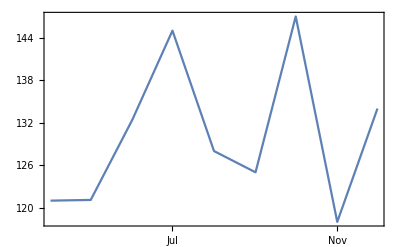

```mathematica
assoc=<|"2017-4"->121,"2017-5"->121.1,"2017-6"->132.4,"2017-7"->145.,"2017-8"->128.,"2017-9"->125.,"2017-10"->147.,"2017-11"->118.,"2017-12"->134.|>;
DateListPlot[assoc]
```

Quick way to convert tables into key value pairs and vice versa.

```mathematica
Association[Rule@@@{{key1,val1},{key2,val2}}]
```

<|key1→val1,key2→val2|>

```mathematica
KeyValueMap[List,%]
```

{{key1,val1},{key2,val2}}

Associations cannot contain different values with identical keys.

```mathematica
<|a->1,b->2,a->3|>
```

<|a→3,b→2|>

Change values associated with a certain key in a list of associations:

```mathematica
assoclist={<|a->3,b->2|>,<|a->1,b->4|>};
assoclist[[All,Key@a]]=0;
assoclist
```

{<|a→0,b→2|>,<|a→0,b→4|>}

Alternatively (which can also be used to append key-value pairs to an association):

```mathematica
<|#,a->10|>&/@assoclist
```

{<|a→10,b→2|>,<|a→10,b→4|>}

## Working with datasets

#### Creating datasets

Datasets can be created by semantic import, or directly from lists or associations:

```mathematica
dataset1=Dataset[data];
dataset1=SemanticImport["data.csv"];
```

Tricks for creating keys: 
Use AssociationThread to create associations. Use pure function to apply this association to multiple rows (have trouble doing it with its function argument):

```mathematica
dataset1=AssociationThread[{"time stamp","col1","col2"}->#]&/@data//Dataset
```

Convert regular tables into dataset with hierarchical row label:

```mathematica
dataset2=AssociationThread[{"row key 1","row label 2"}->AssociationThread[{"time stamp","col1","col2"}->#]&/@table]//Dataset
```

#### Manipulating

datasets can be indexed just like a matrix, but use [ ] to take parts from it, and rows & columns can be specified using key name. 
see documentation.

Create new columns (operation on rows):

```mathematica
ds[All,<|#,"col3"->#col1+#col2,"col4"->#col1*#col2|>&]
```

One use is to convert time stamp from string to objects.
Use similar technique to rename columns (essentially creating new columns):

```mathematica
dataset[All,<|"new col1"->"col1","new col2"->"col2"|>]
```

Apply (map) operation on rows/entries of specified column(s):
(also operation on rows)

pure functions can be applied properly to different keys of datasets by using ->.

```mathematica
dataset1[All,{"key1"->g,"key2"->#&}]; (* this CANNOT be properly evaluated   ! *)
dataset1[All,{"key1"->g,"key2"->(#&)}]; (* make sure the function if properly parenthesized *)
```

All other columns not operated on are still selected.

Apply function to extracted column(s):
(operation on extracted columns)

```mathematica
dataset[Total,{"col1","col2"}]
dataset[Total,{1,2}]
(*cannot mix names and number index of columns in part specification!*)
```

Extract and output into lists or tables:

```mathematica
dataset[All,{"key1","key2"}]//Normal//Values
(*or*)
dataset[[Values,Values]]//Normal
```

Delete columns of a dataset:

```mathematica
Delete[#,{{Key[a]},{"b"}}]&/@dataset
(*delete named columns by applying the operation to each row of a dataset*)
```

Group rows:

select rows first, then select columns, then group.

```mathematica
dataset[GroupBy[OddQ[#a]&],Select[#a>2&],{"a","b"}]
```

select rows first,  then group, then apply function to columns.

```mathematica
dataset[GroupBy[OddQ[#a]&],Select[#a>2&],{"a"->(#*2&)}]
```

#### Merge and extract data

Join using values of a key (usually column name): convert to associations and use JoinAcross. Need to make sure time stamp format are the same. 
Operation needs to convert dataset into associations first (by function Normal).

```mathematica
JoinAcross[dataset1//Normal,dataset2//Normal,Key["date"],"Outer",KeyCollisionFunction->Right]//Dataset;
(*join multiple datasets/associations*)
joinedSet=Fold[JoinAcross[#1,#2,Key["Tm"]]&,assoc1,{assoc2,assoc3}]//Dataset
```

Join using named rows:

```mathematica
Merge[{dataset1//Normal,dataset2//Normal},Association]
```

#### Exporting

Structured dataset can sometimes be directed exported to .csv file (so far seems that other formats don’t work).

Strings as well as numbers can be included, but datasets with objects or nested structures (such as lists) cannot be properly exported. 
Best is to reduce them to normal forms, extract values into tables, then export. 
One problem: time is exported not as string, but as time format in excel, it can still be imported as string in Mathematica, but may or may not be imported correctly in other programs.

```mathematica
Export["data01.csv",dataSet1,"CSV"]; (*actually specification of "CSV" is not needed here*)
Export["data01.dat",dataSet1];
```

To export datasets with date objects, convert them to string first (usually time stamp is the first element in the lists):
Exporting to local disks is generally faster.

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"dataset.csv"}],Map[MapAt[DateString[#,{"Day","/","Month","/","Year"," ","Hour",":","Minute"}]&,#,1]&,data],"CSV"]
```

#### Misc.

When using specialized forms of query (e.g. dataset[All, f]), function within “[ ]” applies to extracted associations from each row of the dataset (in the form of associations, unless each row contains another dataset object), so not in the form of datasets. So operations like below will not work:

```mathematica
dataset[All,#[Total,"col1"]&]
(*instead, should be written as below if really want to use dataset operations on each row entry:*)
dataset[All,(Dataset[#][Total,"col1"]//Normal)&]
(*or just construct a new dataset directly*)
dataset[All,<|"col1"->Total[#[[All,"col1"]]]|>&]
```

Acceptable forms of referral to named items in pure function form:
note: needs to make sure the # being referred to is an association, NOT a dataset, otherwise referral may not work properly.

```mathematica
<|#,"col3"->(#"col_1"/#"col_2")|>& (*no space within the strings*)
<|#,"col3"->#col1+#col2|>&
<|#,"col3"->#["col 1"]+#["col 2"]|>& (*for those column names with space inside*)
```

## Working with SQL database

## Basics

Connect to database on local machine:

```mathematica
Needs["DatabaseLink`"];
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","localhost/testdb"],"Username"->"root","Password"->"data@work.88"]
```

SQLConnection[…]

```mathematica
conn=OpenSQLConnection[JDBC["Microsoft Access(UCanAccess)","testdb.accdb"]]
```

Close database connection after use:

```mathematica
CloseSQLConnection[conn]
```

Inspection:

```mathematica
SQLTables[conn]
```

{SQLTable[students,TableType→BASE TABLE]}

```mathematica
SQLColumns[conn,"students"]
```

{SQLColumn[{students,ID},DataTypeName→INT,DataLength→10,Default→Null,Nullable→0],SQLColumn[{students,firstName},DataTypeName→VARCHAR,DataLength→20,Default→Null,Nullable→0],SQLColumn[{students,lName},DataTypeName→VARCHAR,DataLength→45,Default→Null,Nullable→1],SQLColumn[{students,class},DataTypeName→VARCHAR,DataLength→45,Default→Null,Nullable→1],SQLColumn[{students,age},DataTypeName→INT UNSIGNED,DataLength→10,Default→Null,Nullable→1]}

```mathematica
SQLSelect[conn,"students"];
SQLSelect[conn,"students","ShowColumnHeadings"->True]//TableForm
```

ID | firstName | lName | class | age
1 | adam | b | c | 19
2 | da | db | s33 | 22
3 | tess | bahh | physic | 24
4 | <tess> | bahh | physics | 21

```mathematica
SQLExecute[conn,"SELECT `1` FROM `2`", {SQLArgument[SQLColumn["firstName"],SQLColumn["lName"],SQLColumn["age"]], SQLTable["students"]}]
```

Make changes (these operations support batch mode for faster operation, insert multiple entries by passing a list of list):

```mathematica
SQLInsert[conn,"students",{"firstName","lName","class","age"},{"adam","puu","Day6",29}]
(*default is batch mode, fast method*)

SQLExecute[conn,"INSERT INTO `testdb`.`students` (`firstName`, `lName`, `class`, `age`) VALUES ('hu', 'bil', 'math', '25');"]

(* use place holders in VALUES section, take note the quote symbol is ``, not '', alternatively can also use ? as a plase holder *)
SQLExecute[conn,"INSERT INTO `testdb`.`students` (`firstName`, `lName`, `class`, `age`) VALUES (`1`, `2`, `3`, `4`);",{"hh","leo","omni",29}]

SQLExecute[conn,"INSERT INTO `1` (`2`) VALUES (`3`);",{SQLTable["students"],SQLArgument[SQLColumn["firstName"],SQLColumn["lName"],SQLColumn["class"],SQLColumn["age"]],SQLArgument["hh2","leo2","omni2",29]}]
```

```mathematica
SQLUpdate[conn,"students",{"age"},{28},SQLColumn["age"]>28]
```

Select and get item names based on string pattern tests:

```mathematica
systNames=SQLSelect[conn,"pv_systems",{"system_id"},SQLStringMatchQ[SQLColumn["system_id"],"Sg_Tengeh%"]&&SQLColumn["system_type"]≠"floating sub-array"];
```

Create Tables

```mathematica
SQLCreateTable[conn,SQLTable["TEST3"], 
{
SQLColumn["TINYINTCOL","DataTypeName"->"TINYINT"],
SQLColumn["SMALLINTCOL","DataTypeName"->"SMALLINT"],
SQLColumn["INTEGERCOL","DataTypeName"->"INTEGER"],
SQLColumn["BIGINTCOL","DataTypeName"->"BIGINT"],
SQLColumn["NUMERICCOL","DataTypeName"->"NUMERIC"],SQLColumn["DECIMALCOL","DataTypeName"->"DECIMAL"],
SQLColumn["FLOATCOL","DataTypeName"->"FLOAT"],
SQLColumn["REALCOL","DataTypeName"->"REAL"],
SQLColumn["DOUBLECOL","DataTypeName"->"DOUBLE"],SQLColumn["BITCOL","DataTypeName"->"BIT"],
SQLColumn["LONGVARBINARYCOL","DataTypeName"->"LONGVARBINARY"],
SQLColumn["VARBINARYCOL","DataTypeName"->"VARBINARY","DataLength"->100],
SQLColumn["BINARYCOL","DataTypeName"->"BINARY"],
SQLColumn["LONGVARCHARCOL","DataTypeName"->"LONGVARCHAR"],
SQLColumn["VARCHARCOL","DataTypeName"->"VARCHAR","DataLength"->5],SQLColumn["CHARCOL","DataTypeName"->"CHAR","DataLength"->3],
SQLColumn["DATECOL","DataTypeName"->"DATE"],SQLColumn["TIMECOL","DataTypeName"->"TIME"],
SQLColumn["TIMESTAMPCOL","DataTypeName"->"TIMESTAMP"],
SQLColumn["OBJECTCOL","DataTypeName"->"OBJECT"]
}]
```

## Basic analysis

## Time series inspection

### Smoothing

Obtain moving average in a general way by moving map functions to time series data:

```mathematica
MovingMap[Median,timeSeriesObject,Quantity[10,"Days"]]
```

#### Spline Fitting

```mathematica
SplineModel[data_,deg_,knots_]:=Block[{basis,allKnots},basis=Array[x^#&,deg+1,0]~Join~Table[BSplineBasis[{deg,knots},i,x],{i,0,Length[knots]-deg-2}];
LinearModelFit[data,basis,x]];
```

Example:

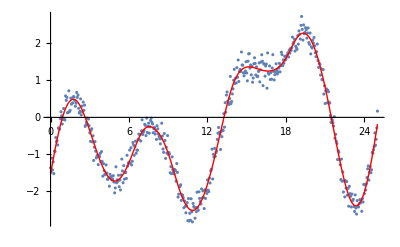

```mathematica
SeedRandom[249304];data=Table[{i,RiemannSiegelZ[i]+Sin[i]+RandomReal[NormalDistribution[0,.2]]},{i,0,25,.05}];

knots=Range[0,25,1];
mod=SplineModel[data,3,knots];

Show[ListPlot[data],Plot[mod[x],{x,0,25},PlotStyle->Directive[Red,Thick]]]
```

## Distribution & patterns

### Histogram

```mathematica
Histogram[data,Automatic,"Probability",
Frame->True,
FrameLabel->{"variable","probability"},
Axes->False,
LabelStyle->{FontFamily->"Helvetica",FontSize->15,FontWeight->Bold,FontColor->Black},
ImageSize->Large]
```

## Clustering

## Others

## Interpolation

Interpolation for a 2D table:

```mathematica
(*this example assumes world data with lat grid 89.5 to -89.5 and longitude grid -179.5 to 179.5*)
Interpolation[Flatten[Table[{{x,y},data2D[[90.5-x,y+180.5]]},{x,89.5,-89.5,-1},{y,-179.5,179.5,1}],1]];
```

Sometimes 2D interpolation can get very slow. In such cases it’s better to interpolate manually as below:

Construct refined table from existing 2D table:

```mathematica
Transpose[Table[Interpolation[#,InterpolationOrder->1][x],{x,1,180,0.5}]&/@Transpose[Table[Interpolation[#,InterpolationOrder->1][x],{x,1,360,0.5}]&/@data2D]]
```